```mathematica
(* Import data from Johns Hopkins *)
HopkinsConfirmed = Drop[Import["~/Documents/Wolfram Mathematica/covid19be/johns-hopkins-data/time_series_covid19_confirmed_global.csv",CharacterEncoding->"UTF8"],1];

HopkinsRecovered = Drop[Import["~/Documents/Wolfram Mathematica/covid19be/johns-hopkins-data/time_series_covid19_recovered_global.csv",CharacterEncoding->"UTF8"],1];

HopkinsDeaths = Drop[Import["~/Documents/Wolfram Mathematica/covid19be/johns-hopkins-data/time_series_covid19_deaths_global.csv",CharacterEncoding->"UTF8"],1];

CountryList=AlphabeticSort[DeleteDuplicates[Transpose[HopkinsConfirmed][[2]]]];
```

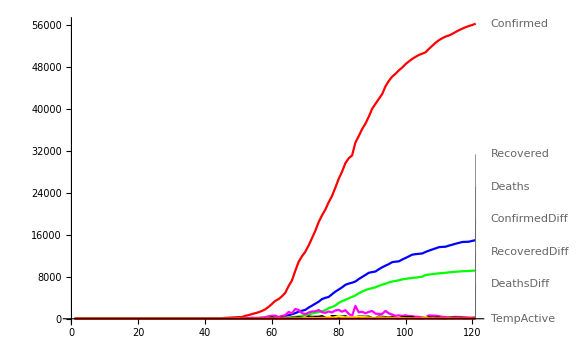

```mathematica
(* Data for countries can be split over multiple rows in the data from Hopkins *)
DataByCountry = Table[{},{i,1,Length[CountryList]}];
NumberOfDays = Length[Transpose[HopkinsConfirmed]]-4;

For[country = 1, country ≤ Length[CountryList],country++,
TempConfirmed=Table[0,{i,1,NumberOfDays}];
TempRecovered = Table[0,{i,1,NumberOfDays}];
TempDeaths = Table[0,{i,1,NumberOfDays}];
For[row=1,row≤ Length[HopkinsConfirmed],row++,
If[StringMatchQ[CountryList[[country]], HopkinsConfirmed[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempConfirmed = TempConfirmed + Drop[HopkinsConfirmed[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsRecovered],row++,
If[StringMatchQ[CountryList[[country]], HopkinsRecovered[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempRecovered= TempRecovered + Drop[HopkinsRecovered[[row]],4];
]
];

For[row=1,row≤ Length[HopkinsDeaths],row++,
If[StringMatchQ[CountryList[[country]], HopkinsDeaths[[row,2]]],
(* Country name of ConfirmedByCountry matches current row *)
TempDeaths = TempDeaths + Drop[HopkinsDeaths[[row]],4];
]
];
TempConfirmedDiff=TempConfirmed-Drop[Join[{0},TempConfirmed],-1];
TempRecoveredDiff=TempRecovered-Drop[Join[{0},TempRecovered],-1];
TempDeathsDiff=TempDeaths-Drop[Join[{0},TempDeaths],-1];
DataByCountry[[country]]= {ToString[CountryList[[country]]],TempConfirmed,TempRecovered,TempDeaths,TempConfirmedDiff,TempRecoveredDiff,TempDeathsDiff,TempActive};
]
ListPlot[Drop[DataByCountry[[17]],1],PlotRange->All,Joined->True,PlotStyle->{Red,Blue,Green,Magenta,Black,Yellow}, PlotLabels->{"Confirmed","Recovered","Deaths","ConfirmedDiff","RecoveredDiff","DeathsDiff","TempActive"}, ImageSize->Large]
```

```mathematica
Window =3;
vandaag = 120;
n0 = 11400000;
i0=100;
gamma=1/12.4;
delta = 1./500;
listr0 = {};
For[day = 1, day <= Length[DataByCountry[[17]][[2]]] + 60, day++,
  listr0 = Join[listr0, {{day, 4.3}}];
  ];
```

```mathematica
SIR[dday_] := (
n=n0;
i=i0;
r=0;
m=0;
c=r+r+m;
s = n-i-r-m;
cost = 0;
For[sirday=1,sirday≤ dday, sirday++,
lambda = gamma * listr0[[sirday]][[2]];
ds = -lambda i *(s/n);
di = lambda i * (s/n) -gamma i - delta i;
dr = gamma i;
dm = delta i;
dc=di +dr+dm;
s+=ds;
i+=di;
r+=dr;
m+=dm;
c+=dc;
n=s+i+r;
If[sirday≤ Length[DataByCountry[[17]][[2]]],
cost = cost + (c-DataByCountry[[17]][[2]][[sirday]])^2;];
];
Return[{s,i,r,m,c,cost,di}];
);
```

```mathematica
For[day=1,day≤Length[DataByCountry[[17]][[2]]]-Window,day++,
bestr0=listr0[[day]][[2]];
bestcost=SIR[day+Window][[6]];
For[kr0 = 0.02,kr0≤7,kr0=kr0+0.05,
(* set this possible r0 for all folliwing days and see what the cost is *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] = kr0;];
temp=SIR[day + Window];
If[temp[[6]]<bestcost,bestcost=temp[[6]];bestr0=kr0;];
];

(* We found a good r0 for this day, set it for all the following days *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] =bestr0;];
];
```

```mathematica
lists={};
listi={};
listr={};
listm={};
listc={};
listdi={};
For[day=1,day≤Length[DataByCountry[[17]][[2]]]+60,day++,
temp=SIR[day];
lists=Append[lists,{day,temp[[1]]}];
listi=Append[listi,{day,temp[[2]]}];
listr=Append[listr,{day,temp[[3]]}];
listm=Append[listm,{day,temp[[4]]}];
listc=Append[listc,{day,temp[[5]]}];
listdi=Append[listdi,{day,temp[[7]]}];
];
```

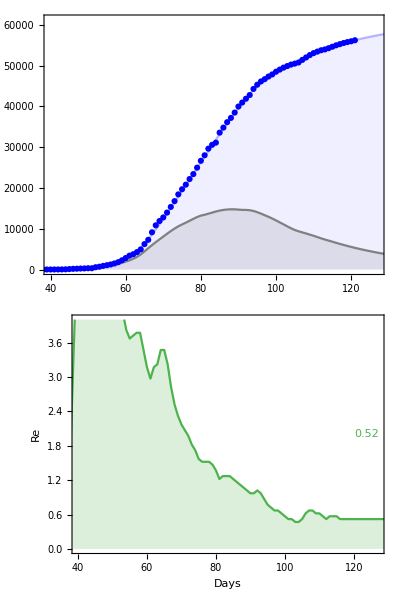

```mathematica
plotFinalR0 = Graphics[{Text[Style[listr0[[-1]][[2]], Medium,RGBColor[0.3,0.7,0.3]],{120,2},{Left,Center}]}];

plotModel=ListPlot[{listi,listc,DataByCountry[[17]][[2]]},PlotRange->{{40,vandaag+7},All},Joined->{True,True,False},Filling->{1-> Bottom,2->Bottom},PlotStyle->{Gray,RGBColor[0.7,0.7,1],Blue},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thickness[0.002],13],AspectRatio->1/1,ImageSize->600];

plotR0=ListPlot[listr0,Joined->True,Filling->{1->Bottom},PlotStyle->RGBColor[0.3,0.7,0.3],FrameLabel->{"Days","Re"},FrameStyle->Directive[Thickness[0.002],13],Frame->True,FrameTicks->Automatic,AspectRatio->1/8,PlotRange->{{40,vandaag+7},{0,4}},ImageSize->600];

Multicolumn[{Show[plotModel,ImagePadding->{{40,1},{20,1}}],Show[{plotR0,plotFinalR0},ImagePadding->{{40,1},{40,5}}]},1]
```